# Lab 9: Spectroscopy

J.R. Powers-Luhn
jpowersl@vols.utk.edu
Station 4
Partner: Eric Francis

```mathematica
datafolder=NotebookDirectory[]<>"data/";
```

```mathematica
loaddata[filename_]:=ToExpression[StringSplit[Import[datafolder<>filename],"\n"][[13;;-17]]]
```

Assembled NaI(Tl) Detector: Setup and Spectral Analysis

1. For each spectrum collected, determine the peak position by averaging over the peak. The answer should be in channel number.

Background

```mathematica
file="background2.Spe";
bgdata=loaddata[file];
bgtime=
```

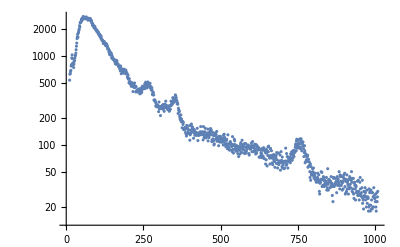

```mathematica
ListLogPlot[bgdata]
```

Cs-137

```mathematica
file="cs137part1-15.Spe";
data=loaddata[file];
pk=FindPeaks[data,50,10^-58,400]
```

{{74,573},{353,587}}

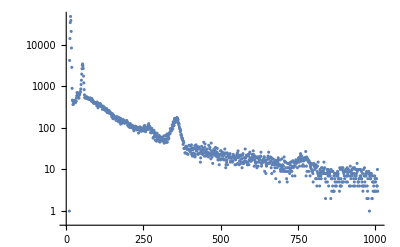

```mathematica
ListLogPlot[data]
```

Co-60

```mathematica
file="co60part1.Spe";
data=loaddata[file];
pk=FindPeaks[data,50,10^-58,400]
```

```mathematica
ListLogPlot[data]
```

-Graphics-

Cd-109

```mathematica
file="cd109part1.Spe";
data=loaddata[file];
pk=FindPeaks[data,50,10^-58,400]
```

{{14,47494}}

```mathematica
ListLogPlot[data]
```

-Graphics-

Ba-133

```mathematica
file="ba133part1.Spe";
data=loaddata[file];
pk=FindPeaks[data,50,10^-58,400]
```

{{19,45531}}

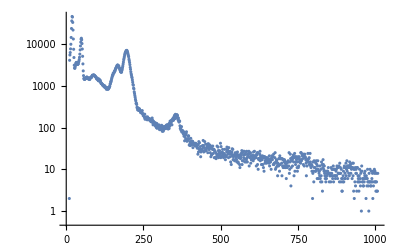

```mathematica
ListLogPlot[data]
```

2. Make a properly formatted table in Mathematica listing the source, the emission energy, and the peak position determined from step one.

3. From the data within the table, conduct a first order polynomial fit on the data to find the voltage to energy conversion.

4. Now try a second order polynomial.

5. Plot the data (channel number vs. energy) along with the first and second order polynomial fits on the same, properly formatted, plot.

6. In a text-style cell, discuss whether the first order or second order polynomial fit better describes the data and why. Further discuss how non-proportional the NaI(Tl) detector is.

7. Using the best fit to the data, convert the spectrum from counts vs. channel number to counts vs. energy for the Cs-137 spectrum.

8. Plot the Cs-137 energy spectrum against the HPGe and CZT Cs-137 energy spectra.

9. Below the plot, and in a text-style cell, discuss what you see on the plot in step 8. Describe the shape of each spectra and the resolution of each.

The Need for a Preamplifier

1. For each spectrum collected with and without the preamplifier in the pulse processing chain, determined the full energy peak position in channel number units.
	a. Note: The peak may drift away for larger shaping time constants, and may even disappear. If this happens, label it as “Not Present”.

2. Make a properly formatted table in Mathematica that includes the shaping time, peak position with preamp, and peak position without preamp.

3. Investigating the data contained within the table, discuss the trends observed with and without the preamplifier present in a text-style cell. Theorize the origin of the differences between the two datasets, [sic] and further comment on why the use of a preamplifier is necessary.

Integral Pulse Height Spectrum

1. Make a 2D list of data of LLD (x-value) and counts (y-value).

2. Change the collected Cs-137 spectra in the first part of the lab from counts vs. channel number to counts vs. voltage.

3. Plot the 2D list of data, which is a crude integral pulse height spectrum, against the quality differential pulse height spectrum.
	a. You may try and connect the dots between data points using the “Interpolation” option in Mathematica for graphing purposes so it is easier to compare the two spectra.

4. Using the drawing tools, correlate the shape of each spectra with each other.